169757. l^2 S v^2

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{v→-37.99/l},{v→37.99/l}}

{37.99/l}

53295.9 l^2 SALu vAlu^2

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{vAlu→-81.0377/l},{vAlu→81.0377/l}}

{81.0377/l}

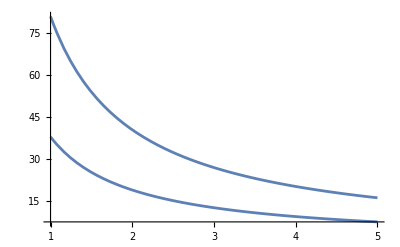

```mathematica
ClearAll["Global`*"];
gestoscMiedzi = 8.6 * 1000 ;
gestoscAluminium = 2.7 * 1000 ;
Rm =2.45*10^8;
Ralu =3.5*10^8;
omegaMiedz = 2*Pi*v;
F = Integrate[r*omegaMiedz^2*gestoscMiedzi*S,{r, 0, l}]

A = Solve[F/S == Rm, v]
czestotliwosc = v/.A;
rozw = Cases[czestotliwosc, x_Real*(y_Symbol)^_/;(x>0)]

rys1 = Plot[v /. v ->rozw[[1]], {l, 1 ,5}, DisplayFunction->Identity, PlotRange->All];



omegaAlu = 2*Pi*vAlu;
FAlu = Integrate[r*omegaAlu^2*gestoscAluminium*SALu,{r, 0, l}]
AluRownanie = Solve[FAlu/SALu == Ralu, vAlu]
czestotliwoscALu = vAlu/.AluRownanie;
rozAlu = Cases[czestotliwoscALu, x_Real*(y_Symbol)^_/;(x>0)]
rys2 = Plot[vAlu /. vAlu ->rozAlu[[1]], {l, 1 ,5},
DisplayFunction->Identity, PlotRange->All
];
Show[rys1, rys2, DisplayFunction -> $DisplayFunction]
```